```mathematica
Clear["Global`*"]
Needs["Developer`"]
Needs["CCompilerDriver`"]
```

## Import

```mathematica
Needs["Developer`"]
```

```mathematica
ClearAll[ReadMSHFile,DumpMSHFileTo2DATFiles,ReadMSHFileFrom2DATFiles]
ReadMSHFile[filename_]:=Module[{i,SkipStreamNumbers,ReadStreamNumbers,meshStr,nNodes,nodesTable,nElements,nPoints,nLines,nTriangles,trianglesTable,temp},
SkipStreamNumbers=Skip[#1,Table[Number,{i,Range[#2]}]]&;
ReadStreamNumbers=Read[#1,Table[Number,{i,Range[#2]}]]&;
meshStr=OpenRead[filename];
Find[meshStr,"$Nodes"];
nNodes=Read[meshStr,Number];
nodesTable=ConstantArray[0.0,{nNodes,2}];
For[i=1,i≤nNodes,i++,
Skip[meshStr,Number];
nodesTable⟦i⟧=N@ReadStreamNumbers[meshStr,2];
Skip[meshStr,Number];
];
Find[meshStr,"$Elements"];
nElements=Read[meshStr,Number];
nPoints=0;nLines=0;nTriangles=0;
trianglesTable=ConstantArray[0.0,{nElements,3}];
For[i=1,i≤nElements,i++,
Skip[meshStr,Number];
temp=Read[meshStr,Number];
If[temp==15,nPoints++;SkipStreamNumbers[meshStr,4];];
If[temp==1,nLines++;SkipStreamNumbers[meshStr,5];];
If[temp==2,nTriangles++;SkipStreamNumbers[meshStr,3];trianglesTable⟦nTriangles⟧=N@ReadStreamNumbers[meshStr,3];];
];
trianglesTable=trianglesTable⟦1;;nTriangles⟧;
Close[meshStr];
ToPackedArray/@{nodesTable,Floor@trianglesTable}
]
DumpMSHFileTo2DATFiles[mshfilename_]:=Module[{dir,nodesTable,trianglesTable},
{nodesTable,trianglesTable}=ReadMSHFile[mshfilename];
dir=FileNameJoin[{DirectoryName[mshfilename],FileBaseName[mshfilename]<>".dat"}];
CreateDirectory[dir]//Quiet;
Print["directory created:",dir];
Export[FileNameJoin[{dir,"nodes.dat"}],nodesTable];
Export[FileNameJoin[{dir,"triangles.dat"}],trianglesTable];
Print["exported nodes file: ",FileNameJoin[{dir,"nodes.dat"}]];
Print["exported triangles file: ",FileNameJoin[{dir,"triangles.dat"}]];
]
ReadMSHFileFrom2DATFiles[mshfilename_]:=Module[{dir},
dir=FileNameJoin[{DirectoryName[mshfilename],FileBaseName[mshfilename]<>".dat"}];
Print["imported nodes file: ",FileNameJoin[{dir,"nodes.dat"}]];
Print["imported triangles file: ",FileNameJoin[{dir,"triangles.dat"}]];
ToPackedArray/@{N@Import[FileNameJoin[{dir,"nodes.dat"}]],Import[FileNameJoin[{dir,"triangles.dat"}]]}
]
```

Read directly from the .msh file and check

```mathematica
dir=FileNameJoin[{NotebookDirectory[],"../msh"}]
```

/home/qzmfrank/codes/rte2dvis/notebook/../msh

```mathematica
{nodesRaw,trianglesRaw}=ReadMSHFile[FileNameJoin[{dir,"square26.msh"}]];
PackedArrayQ/@{nodesRaw,trianglesRaw}
```

{True,True}

Dump the .msh file data into two separate .dat files

```mathematica
DumpMSHFileTo2DATFiles[FileNameJoin[{dir,"square26.msh"}]]
```

directory created:/home/qzmfrank/codes/rte2dvis/notebook/../msh/square26.dat

exported nodes file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square26.dat/nodes.dat

exported triangles file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square26.dat/triangles.dat

Read the two .dat files and check

```mathematica
{nodesRaw2,trianglesRaw2}=ReadMSHFileFrom2DATFiles[FileNameJoin[{dir,"square26.msh"}]];
PackedArrayQ/@{nodesRaw2,trianglesRaw2}
Total[Norm/@#]&/@{nodesRaw2-nodesRaw,trianglesRaw2-trianglesRaw}
```

imported nodes file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square26.dat/nodes.dat

imported triangles file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square26.dat/triangles.dat

{True,True}

{0.,0}

## Ray Tracing

```mathematica
ClearAll[InTriangle,PickTriangle]
InTriangle[v_,ptn_]:=Module[{det,v0,v1,v2,a,b},
det=#1⟦1⟧#2⟦2⟧-#1⟦2⟧#2⟦1⟧&;
v0=ptn⟦1⟧;
v1=ptn⟦2⟧-v0;
v2=ptn⟦3⟧-v0;
a=(det[v,v2]-det[v0,v2])/det[v1,v2];
b=-(det[v,v1]-det[v0,v1])/det[v1,v2];
a>0.0&&b>0.0&&a+b<1.0
]
PickTriangle[v_]:=Module[{n},For[n=1,n≤Ns,n++,If[InTriangle[v,pt⟦n⟧],Break[]]];n]
ClearAll[HalfLineTriangleSegmentC,P0,PT,alpha]
HalfLineTriangleSegmentC=Compile[{{alpha,_Real},{p,_Real,1},{pt,_Real,2}},
Module[{n,d,ds,pts,k,t},
n={Cos[alpha],Sin[alpha]};d=Det[{#-p,n}]&/@pt;ds=Sort[d];
If[ds⟦1⟧ds⟦3⟧≤0.0&&!(Abs[ds⟦1⟧]<1.0*10^-15&&Abs[ds⟦3⟧]<1.0*10^-15),0.0;,Return[0.0];];
k={0,0,0};
k⟦1⟧=Position[d,ds⟦1⟧]⟦1,1⟧;k⟦3⟧=Position[d,ds⟦3⟧]⟦1,1⟧;
k⟦2⟧=Delete[Range[3],{{k⟦1⟧},{k⟦3⟧}}]⟦1⟧;pts=pt⟦k⟦#⟧⟧&/@Range[3];
t=If[ds⟦1⟧*ds⟦2⟧≥0,
{-Det[{pts⟦3⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦3⟧-pts⟦1⟧,n}],-Det[{pts⟦3⟧-pts⟦2⟧,p-pts⟦2⟧}]/Det[{pts⟦3⟧-pts⟦2⟧,n}]},
{-Det[{pts⟦2⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦2⟧-pts⟦1⟧,n}],-Det[{pts⟦3⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦3⟧-pts⟦1⟧,n}]}
];
t=Sort[t];
t⟦1⟧=Max[t⟦1⟧,0.0];
t⟦2⟧=Max[t⟦2⟧,0.0];
t⟦2⟧-t⟦1⟧
]
(*,CompilationTarget:>"C"*)
];
P0={0,-√3/2}//N;PT={{0,0},{1,0},{1/2,√3/2}}//N;alpha=π/3//N;
Plot[HalfLineTriangleSegmentC[alpha,P0,PT],{alpha,0,2π},AxesOrigin->{0,0}];
```

## Solver

```mathematica
Needs["Developer`"]

ClearAll[filename,mus,mua,mut,g,Phasef,Phasef1,Phasef2,PhaseFunc,PhaseFunc1,phis,Nd,padding]
(*filename=FileNameJoin[{NotebookDirectory[],"../msh","t4.msh"}];*)
filename=FileNameJoin[{NotebookDirectory[],"../msh","square162.msh"}];
DumpMSHFileTo2DATFiles[filename];
(*
mus[{x_,y_}]:=2x^2+y+Exp[-0.1x-0.2y]
mua[{x_,y_}]:=x+3y^2-Exp[-0.5x+y^2]
*)
mus[{x_,y_}]:=2Log[2]
mua[{x_,y_}]:=Log[2]
mut[{x_,y_}]:=mua[{x,y}]+mus[{x,y}]
g=0.6;
Phasef1[m_]:=g^Abs[m]
Phasef2[m_]:=If[m==0,1.0,0.0]
Phasef=Phasef1;
PhaseFunc1=Compile[{{phi,_Real}},(1.0-g^2)/(2π(1+g^2-2g Cos[phi]))(*,CompilationTarget:>"C"*)];
PhaseFunc=PhaseFunc1;
phis=0;
Nd=30;
padding=32;

ClearAll[iG,iL,ToCmplxPckdArry]
iG[{n_,m_},{Ns_,Nd_}]:=(n-1)*(2Nd+1)+m+Nd+1
iL[ng_,{Ns_,Nd_}]:={IntegerPart[(ng-1)/(2Nd+1)+1],Mod[ng-Nd-1,(2Nd+1),-Nd]}
ToCmplxPckdArry=ToPackedArray[N[Re[#]]]+ⅈ ToPackedArray[N[Im[#]]]&;

ClearAll[TriPtPreCalc,CntrPreCalc,r2rRPreCalc,SignedAreaPreCalc]
TriPtPreCalc[p_,t_]:=p⟦#⟧&/@t//ToPackedArray
CntrPreCalc[pt_]:=(Total/@pt)/3.0//ToPackedArray
r2rRPreCalc[cntr_]:=Outer[If[#1<#2,Norm[Subtract@@cntr⟦{#1,#2}⟧],0.0]&,Range[Length[cntr]],Range[Length[cntr]]]//ToPackedArray//#+#ᵀ&
SignedAreaPreCalc[pt_]:=pt//Map[{#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦3⟧}&,#]&//Map[#⟦1,1⟧#⟦2,2⟧-#⟦1,2⟧#⟦2,1⟧&,#]&//ToPackedArray//Times[#,0.5]&;

ClearAll[Np,p,t,Nm,Ns,Ng,gTbl,iGTbl,iLTbl,pt,cntr,r2rR,area,Tpt,Tcntr,Tr2rR,Tarea]
{p,t}=ReadMSHFileFrom2DATFiles[filename];

(*
(*symmetrize the geometry w.r.p.t. y=0*)
Np=Length[p];
t=t//Join[#,Map[#+ConstantArray[Np,3]&,t]]&;
p=Join[p,{#⟦1⟧,-#⟦2⟧}&/@p];
Np=Length[p];
(*end of symmetrization*)
*)

(*
(*symmetrize the geometry w.r.p.t. x=0*)
Np=Length[p];
t=t//Join[#,Map[#+ConstantArray[Np,3]&,t]]&;
p=Join[p,{-#⟦1⟧,#⟦2⟧}&/@p];
Np=Length[p];
(*end of symmetrization*)
*)

Np=Length[p];Ns=Length[t];Nm=2Nd+1;
Module[{n=Mod[Nm,padding]},If[n≠0,Nm=Nm+padding-n;Nd=Floor[(Nm-1)/2];];];
Ng=Ns(2Nd+1);
Print["{p,t}=",PackedArrayQ/@{p,t}];
Print["{Ns,Nd,Nm,Ng}=",{Ns,Nd,Nm,Ng}];
gTbl=Phasef/@Range[-Nd,Nd]//ToPackedArray;
iGTbl=Table[iG[{n,m},{Ns,Nd}],{n,Ns},{m,-Nd,Nd}]//ToPackedArray;
iLTbl=iL[#,{Ns,Nd}]&/@Range[Ng]//ToPackedArray;
Print["{gTbl,iGTbl,iLTbl}=",PackedArrayQ/@{gTbl,iGTbl,iLTbl}];
Tpt=(pt=TriPtPreCalc[p,t];)//AbsoluteTiming//#⟦1⟧&;
Tcntr=(cntr=CntrPreCalc[pt];)//AbsoluteTiming//#⟦1⟧&;
Tr2rR=(r2rR=r2rRPreCalc[cntr];)//AbsoluteTiming//#⟦1⟧&;
Tarea=(area=SignedAreaPreCalc[pt];)//AbsoluteTiming//#⟦1⟧&;
Print["{Tpt,Tcntr,Tr2rR,TsignedArea,Tarea,TRc}=",{Tpt,Tcntr,Tr2rR,Tarea}//{Total[#],#}&];
Print["{pt,cntr,r2rR,signedArea,area,Rc}=",PackedArrayQ/@{pt,cntr,r2rR,area}];
```

directory created:/media/MyData/codes/rte2dvis/notebook/../msh/square162.dat

exported nodes file: /media/MyData/codes/rte2dvis/notebook/../msh/square162.dat/nodes.dat

exported triangles file: /media/MyData/codes/rte2dvis/notebook/../msh/square162.dat/triangles.dat

imported nodes file: /media/MyData/codes/rte2dvis/notebook/../msh/square162.dat/nodes.dat

imported triangles file: /media/MyData/codes/rte2dvis/notebook/../msh/square162.dat/triangles.dat

{p,t}={True,True}

{Ns,Nd,Nm,Ng}={162,31,64,10206}

{gTbl,iGTbl,iLTbl}={True,True,True}

{Tpt,Tcntr,Tr2rR,TsignedArea,Tarea,TRc}={0.07248,{0.00018,0.00016,0.0717,0.00044}}

{pt,cntr,r2rR,signedArea,area,Rc}={True,True,True,True}

```mathematica
ClearAll[Draw2Trig]
Draw2Trig[n_,np_]:=Show[
ListPlot[pt⟦n⟧,PlotRange->{{0,1},{0,1}},PlotStyle->{Blue,PointSize[Large]},Epilog->{Blue,Line[{pt⟦n,1⟧,pt⟦n,2⟧,pt⟦n,3⟧,pt⟦n,1⟧}],Red,Line[{pt⟦np,1⟧,pt⟦np,2⟧,pt⟦np,3⟧,pt⟦np,1⟧}]}],
ListPlot[pt⟦np⟧,PlotStyle->{Red,PointSize[Large]}]
]
```

```mathematica
ClearAll[tt]
tt=Table[t⟦i,j⟧-1,{i,Dimensions[t]⟦1⟧},{j,3}];
tt//Flatten//Max
```

97

```mathematica
B1HomoFull=LibraryFunctionLoad[lib,"BHomoFull_MLL",{{Real,3,"Constant"},Integer,Integer,Integer,Integer,Integer,Integer},{Real,3,"Shared"}];
```

## Homo Z=A+B, V

### LibraryLink

LegendreRule[order,a,b]
	order	integer		>0
	a,b	real		b>a

DunavantRule[rule,{{0,0},{0,1},{1,0}}]
	rule	integer		1<=rule<=21

ArcSinhRule[p,p0,qu,qv]
	p	=	triangle being integrated
	p0	=	singular point
	qu	=	LegendreRule[nu,0,1]
	qv	=	LegendreRule[nv,0,1]

```mathematica
Needs["CCompilerDriver`"]
ClearAll[cflags,dir,incdir,libdir,xlib,src,lib]
cflags="-O3 -Wall -m64";
dir=FileNameJoin[{NotebookDirectory[],"../src/mll"}];
incdir="/opt/intel/mkl/include";
libdir="/opt/intel/mkl/lib/intel64";
xlib="";
(*xlib={"fftw3","mkl_core","mkl_intel_lp64","mkl_sequential","pthread","m"};*)
(*xlib="-lmkl_intel_lp64 -lmkl_core -lmkl_sequential -lpthread -lm";*)
(*xlib={"-lmkl_intel_lp64","-lmkl_core","-lmkl_sequential;","-lpthread","-lm"};*)
src={"wandzura-rule.cpp","dunavant-rule.cpp","legendre-rule.cpp","arcsinh-rule.cpp","mll.cpp"}//Map[FileNameJoin[{dir,#}]&,#]&;
lib=CreateLibrary[src,"libmll","Libraries"->xlib,"IncludeDirectories"->incdir,"LibraryDirectories"->libdir,"CompileOptions"->cflags];
(*lib=CreateLibrary[src,"libmll","Libraries"->"fftw3","CompileOptions"->cflags];*)
ClearAll[cflags,dir,incdir,libdir,xlib,src]
Print["lib=",lib];

ClearAll[LegendreRule,DunavantRule,ArcSinhRule]
LegendreRule=LibraryFunctionLoad[lib,"LegendreRule_MLL",{Integer,Real,Real},{Real,2,"Shared"}];
DunavantRule=LibraryFunctionLoad[lib,"DunavantRule_MLL",{Integer,{Real,2,"Constant"}},{Real,2,"Shared"}];
ArcSinhRule=LibraryFunctionLoad[lib,"ArcSinhRule_MLL",{{Real,2,"Constant"},{Real,1,"Constant"},{Real,2,"Constant"},{Real,2,"Constant"}},{Real,2,"Shared"}];

ClearAll[VHomoFull,BHomo,BHomoFull,BHomoS,BHomoN,HomoMul]
VHomoFull=LibraryFunctionLoad[lib,"VHomoFull_MLL",{{Real,3,"Constant"},Real,Real,Real,Integer,Integer,Integer,Integer,Integer},{Complex,1,"Shared"}];
BHomo=LibraryFunctionLoad[lib,"BHomo_MLL",{{Real,3,"Constant"},Integer,Integer,Integer,Integer,Integer},{Real,3,"Shared"}];
BHomoFull=LibraryFunctionLoad[lib,"BHomoFull_MLL",{{Real,3,"Constant"},Integer,Integer,Integer,Integer,Integer,Integer},{Real,3,"Shared"}];
BHomoS=LibraryFunctionLoad[lib,"BHomoS_MLL",{Integer,Integer,{Real,1,"Constant"},{Real,2,"Constant"}},{Real,1,"Shared"}];
BHomoN=LibraryFunctionLoad[lib,"BHomoN_MLL",{Integer,Integer,{Real,1,"Constant"},{Real,2,"Constant"}},{Real,1,"Shared"}];
HomoMul=LibraryFunctionLoad[lib,"HomoMul_MLL",{{Complex,1,"Constant"},{Real,1,"Constant"},{Real,3,"Constant"},{Real,1,"Constant"},Real,Real},{Complex,1,"Shared"}];

(*
{{"rule","order","positive"}}~Join~Table[{rule,DunavantRule[rule,{{0,0},{0,1},{1,0}}]//Dimensions//#⟦2⟧&,DunavantRule[rule,{{0,0},{0,1},{1,0}}]//Quiet//Map[Positive,#]&//Flatten//DeleteDuplicates//#⟦1⟧&},{rule,20}]//Quiet//TableForm
ClearAll[pp,p0,nu,nv,qu,qv]
LegendreRule[10,0,1]//Quiet;
DunavantRule[10,{{1,0},{3,2},{0,2}}]//Quiet;
pp={{1,0},{0,2},{3,2}};
p0={3,0};
{nu,nv}={3,2};
qu=LegendreRule[nu,0,1]//Quiet;
qv=LegendreRule[nv,0,1]//Quiet;
ArcSinhRule[pp,p0,qu,qv]//Quiet;
ClearAll[pp,p0,nu,nv,qu,qv]
*)

(*
ClearAll[test,raw]
test=LibraryFunctionLoad[lib,"test",{{Complex,1,"Constant"}},{Complex,2,"Shared"}];
raw=RandomComplex[1+ⅈ,500000];
test[raw]//Quiet//AbsoluteTiming//#⟦1⟧&
ClearAll[raw]
*)

(*
LibraryFunctionUnload[test];
LibraryUnload[lib]
*)
```

lib=/home/qzmfrank/.Mathematica/SystemFiles/LibraryResources/Linux-x86-64/libmll.so

```mathematica
{{"rule","order","positive"}}~Join~Table[{rule,DunavantRule[rule,{{0,0},{0,1},{1,0}}]//Dimensions//#⟦2⟧&,DunavantRule[rule,{{0,0},{0,1},{1,0}}]//Quiet//Map[Positive,#]&//Flatten//DeleteDuplicates//#⟦1⟧&},{rule,20}]//Quiet//TableForm
```

```mathematica
LibraryUnload[lib]
```

```mathematica
ClearAll[gg,ϕs,μs,RULE1,RULE2,NU,NV,V]
{gg,ϕs,μs}={0.6,0.0,0.4};
{RULE1,RULE2,NU,NV}={1,5,2Nd+15,3};
V=VHomoFull[pt,gg,ϕs,μs,Nd,RULE1,RULE2,NU,NV]//Quiet//ToPackedArray;
V//Dimensions//Print;
V⟦1;;2Nd+1⟧//TableForm//Print;
ClearAll[gg,ϕs,μs,RULE1,RULE2,NU,NV]
```

### Z=A+B

```mathematica
ClearAll[A,B]
A=2π*area;
SetDirectory[FileNameJoin[{"HOME"/.GetEnvironment["HOME"],"tmp"}]];
<<"B.mx";
ResetDirectory[];
Print["{A,B}=",PackedArrayQ/@{A,B}];
```

{A,B}={True,True}

```mathematica
ClearAll[RULE1,RULE2,NU,NV]
{RULE1,RULE2,NU,NV}={1,15,2Nd+30,3};
(*BHomo[pt,Nd,Nm,RULE,NU,NV]//Quiet;*)
B=BHomoFull[pt,Nd,Nm,RULE1,RULE2,NU,NV]//Quiet//ToPackedArray;
SetDirectory[FileNameJoin[{"HOME"/.GetEnvironment["HOME"],"tmp"}]];
DumpSave["B.mx",B];
ResetDirectory[];
ClearAll[RULE1,RULE2,NU,NV]
```

```mathematica
1,19
```

```mathematica
B0=B;
```

```mathematica
1,13
```

```mathematica
B1=B;
```

```mathematica
1,15
```

```mathematica
B2=B;
```

```mathematica
{n,np}={147,84};
{nd1,nd2}={1,2Nm};
Norm[cntr⟦n⟧-cntr⟦np⟧]//Print;
10^9 B1⟦n,np,nd1;;nd2⟧
10^9 B2⟦n,np,nd1;;nd2⟧;
10^9 B3⟦n,np,nd1;;nd2⟧;
10^9 B4⟦n,np,nd1;;nd2⟧

10^9(B1⟦n,np,nd1;;nd2⟧-B4⟦n,np,nd1;;nd2⟧)//Abs//Max;
```

```mathematica
data=Abs[(B1-B4)/B4]⟦All,All,1⟧;
Position[data,Max[data]]
Max[data]
```

{{147,84}}

52.343

### Test Toeplitz FFT

```mathematica
ClearAll[z,a,b,Z,X]
a=ToeplitzMatrix[{1,2,3,4},{5,6,7,8}]//Quiet;
b=ToeplitzMatrix[{0,8,7,6},{0,4,3,2}];
Z=ArrayFlatten[({{a, b}, {b, a}})];
z=Z⟦All,1⟧;
Z//MatrixForm//Print
X=RandomReal[2,8];
Z.X//Print
InverseFourier[√8 Fourier[z]Fourier[X]]//Print
ClearAll[z,a,b,Z,X]
```

(1 | 6 | 7 | 8 | 0 | 4 | 3 | 2
2 | 1 | 6 | 7 | 8 | 0 | 4 | 3
3 | 2 | 1 | 6 | 7 | 8 | 0 | 4
4 | 3 | 2 | 1 | 6 | 7 | 8 | 0
0 | 4 | 3 | 2 | 1 | 6 | 7 | 8
8 | 0 | 4 | 3 | 2 | 1 | 6 | 7
7 | 8 | 0 | 4 | 3 | 2 | 1 | 6
6 | 7 | 8 | 0 | 4 | 3 | 2 | 1)

{33.3238,30.0073,30.8092,24.6066,27.4801,24.0631,26.1899,25.4562}

{33.3238,30.0073,30.8092,24.6066,27.4801,24.0631,26.1899,25.4562}

### HomoMul and Solve

#### Test - Random Input Vector

```mathematica
ClearAll[μt,μs,X,Y]
μt=Log[2.0]/2;
μs=Log[2.0]/2;
X=RandomComplex[1.0+1.0ⅈ,Ng];
Print["Dim/@{X,A,B,gTbl}=",Map[Length[Dimensions[#]]&,{X,A,B,gTbl}]];
(Y=HomoMul[X,A,B,gTbl,μt,μs]//Quiet;)//AbsoluteTiming//#⟦1⟧&//Print["time HomoMul=",#]&
X⟦1;;10⟧//Print;
Y⟦1;;10⟧//Print;
```

Dim/@{X,A,B,gTbl}={1,1,3,1}

time HomoMul=0.02178

{0.125174+0.698521 ⅈ,0.0240209+0.295213 ⅈ,0.157375+0.751111 ⅈ,0.800372+0.0105667 ⅈ,0.586034+0.821904 ⅈ,0.848442+0.310773 ⅈ,0.410976+0.097969 ⅈ,0.934606+0.850978 ⅈ,0.460052+0.382888 ⅈ,0.150645+0.608998 ⅈ}

{0.00860635+0.0401677 ⅈ,0.00296768+0.0165095 ⅈ,0.00929915+0.0404759 ⅈ,0.0437624+0.00280608 ⅈ,0.0322015+0.044819 ⅈ,0.0467164+0.0173781 ⅈ,0.0227543+0.00658449 ⅈ,0.0512181+0.0463433 ⅈ,0.0257183+0.0217396 ⅈ,0.00884978+0.0337712 ⅈ}

```mathematica
ClearAll[XX]
XX=LinearSolve[HomoMul[#,A,B,gTbl,μt,μs]&,Y,Method->{"Krylov",Method->"GMRES",Tolerance->10^-8,"Preconditioner"->None,MaxIterations->10,"ResidualNormFunction"->Norm}]//Quiet;
Abs[(XX-X)/X]//Flatten//Max
```

0.0000320485

#### V0 - Complete RHS

Plot Fluence

```mathematica
ClearAll[PlotFluenceX0]
PlotFluenceX0[X_,y_]:=Module[{data,coord,index,pltdata},
data=Partition[X,2Nd+1]⟦All,Nd+1⟧//Re;
coord=Table[{x,y},{x,0.01,0.99,0.9/Sqrt[Ns]}]//ToPackedArray;
index=PickTriangle/@coord//ToPackedArray;
pltdata={coord⟦All,1⟧,data⟦index⟧}//Transpose;
(*PackedArrayQ/@{data,coord,index,pltdata}//Print;*)
ListPlot[pltdata,PlotRange->{0,1/(2π)+0.01},AxesLabel->{"x","fluence"}]
]
```

```mathematica
ClearAll[μa,μs,μt,V0,X0]
{μa,μs}={Log[4.0],0.0};
μt=μa+μs;
V0=Table[area⟦n⟧Exp[-ⅈ m phis],{n,Ns},{m,-Nd,Nd}]//Flatten//ToPackedArray;
V0//PackedArrayQ;
X0=LinearSolve[HomoMul[#,A,B,gTbl,μt,μs]&,V0,Method->{"Krylov",Tolerance->10^-20,Method->"GMRES","Preconditioner"->None,MaxIterations->30,"ResidualNormFunction"->Norm}]//Quiet;
Print["Z.X-V: max relative err=",Abs[(HomoMul[X0,A,B,gTbl,μt,μs]-V0)/V0]//Quiet//Flatten//Max];
```

Z.X-V: max relative err=4.79197×10^-14

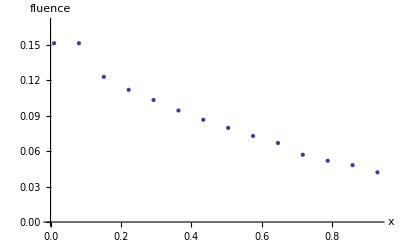

```mathematica
PlotFluenceX0[X0,0.3]
```

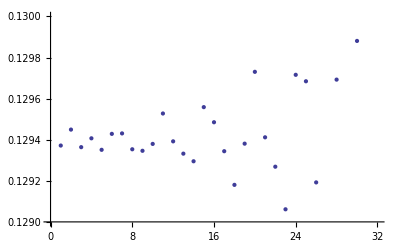

-Graphics-

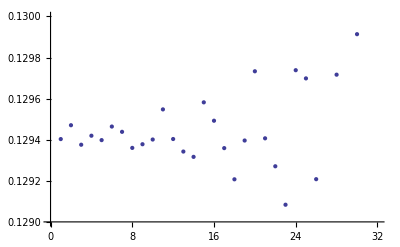

```mathematica
ClearAll[data]
data=Re/@(Partition[X0,2Nd+1]⟦1,Nd+1;;2Nd+1⟧)//ToPackedArray;
ListPlot[data,PlotRange->{0.129,0.130}]
```

#### V1 - leading term extracted

```mathematica
ClearAll[PlotFluenceX1]
PlotFluenceX1[X_,y_]:=Module[{data,coord,base,index,pltdata},
data=Partition[X,2Nd+1]⟦All,Nd+1⟧//Re;
coord=Table[{x,y},{x,0.01,0.99,0.9/Sqrt[Ns]}]//ToPackedArray;
base=1/(2π)Exp[-μt#⟦1⟧]&/@coord//ToPackedArray;
index=PickTriangle/@coord//ToPackedArray;
pltdata=data⟦index⟧+base;
Show[ListPlot[{coord⟦All,1⟧,pltdata}//Transpose,PlotRange->{0,1/(2π)+0.01},AxesLabel->{"x","fluence"}],
Plot[Exp[-μt x]/(2π),{x,0,1},PlotStyle->{Thick,Red,Dashed},PlotRange->{0,1/(2π)+0.01}]]
]
```

```mathematica
ClearAll[RULE1,RULE2,NU,NV,ϕs,μa,μs,μt,V1]
{RULE1,RULE2,NU,NV}={5,19,2Nd+15,3};
{ϕs,μa,μs}={0.0,Log[3.0],2Log[2.0]};
μt=μa+μs;
V1=VHomoFull[pt,g,ϕs,μs,Nd,RULE1,RULE2,NU,NV]//Quiet;
```

```mathematica
ClearAll[X1]
X1=LinearSolve[HomoMul[#,A,B,gTbl,μt,μs]&,V1,Method->{"Krylov",Tolerance->10^-20,Method->Automatic,"Preconditioner"->Automatic,MaxIterations->30,"ResidualNormFunction"->Automatic}]//Quiet;
Print["Z.X1-V1: max relative err=",Abs[(HomoMul[X1,A,B,gTbl,μt,μs]-V1)/V1]//Quiet//Flatten//Max];
```

Z.X1-V1: max relative err=2.65342×10^-13

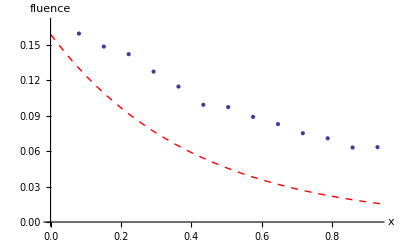

```mathematica
PlotFluenceX1[X1,0.1]
```